```mathematica
Homework for 
       Chapter 5-1&5-2
```

```mathematica
2012311804 이병호/2016314728 정재헌
```

```mathematica
Quit
```

(#1) 다음의 Ricatti 미분방정식의 해를 구하시오.
                                     y'=(y-1)(y+1/x).

```mathematica
Clear["Global'*"]
```

```mathematica
DSolve[y'[x]==(y[x]-1)(y[x]+1/x),y[x],x]
```

{{y[x]→1+(ⅇ^x x)/(-ⅇ^x (-1+x)+C[1])}}

(#2) 작은 도시의 인구를 p(t)로 표시하고 이 함수는 다음의 logistic 방정식 
                                          dp/dt=p(0.2-0.0000005 p) 
        로 표현되고 여기서 t는 월 단위로 측정된다.
        (a) 초기 값이 5000이라면 인구의 극한은 얼마인가?
        (b) 위에서 얻은 극한 값의 반(1/2)에 도달하는 시기(몇 년 후)는 언제인가?

```mathematica
DSolve[{p'[t]==p[t](0.2-0.0000005p[t]),p[0]==5000},p[t],t]//Simplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{p[t]→(400000. ⅇ^(0.2 t))/(79.+1. ⅇ^(0.2 t))}}

```mathematica
s[t]=p[t]/.%[[1]]
Limit[s[t],t->∞]
```

(400000. ⅇ^(0.2 t))/(79.+1. ⅇ^(0.2 t))

400000.

```mathematica
Solve[s[t]==200000,t]
q=t/.%[[1]]
q/12
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→21.8472}}

21.8472

1.8206

즉, 약 1.8년(21.8개월) 후에 절반에 도달한다.

(#3-1) 다음 초기치 문제의 해를 구하시오.
                                     y''+ω^2 y=ⅇ^-t    with   y(0)=1  and y'(0)=0.

```mathematica
Clear["Global'*"]
```

```mathematica
s=DSolve[{y''[t]+w^2 y[t]==Exp[-t], y[0]==1, y'[0]==0}, y[t], t]
```

{{y[t]→(ⅇ^-t (ⅇ^t w^3 Cos[t w]+w Cos[t w]^2+ⅇ^t Sin[t w]+w Sin[t w]^2))/(w (1+w^2))}}

```mathematica
s[[1,1,2]]
```

(ⅇ^-t (ⅇ^t w^3 Cos[t w]+w Cos[t w]^2+ⅇ^t Sin[t w]+w Sin[t w]^2))/(w (1+w^2))

(#3-2) 다음 damped spring-mass system의 steady-state 해의 amplitude를 최대로 만드는 β의 값과 amplitude를 구하고 이 β 값을 직접 방정식에 대입해서 나온 steady-state 해의 amplitude를 비교하시오. 
                         y''+βy'+y=sin(2t)    with   y(0)=0,  y'(0)=0.
                         (In this case    β^2-4≥0.)

```mathematica
Clear["Global'*"]
```

```mathematica
s2:=DSolve[{y''[t]+ β y'[t]+y[t]==Sin[2 t],y[0]==0,y'[0]==0},y[t],t]
```

```mathematica
s2=ExpandAll[s2]
```

{{y[t]→(24 ⅇ^(-(t β)/2-1/2 t √(-4+β^2)))/(-36 √(-4+β^2)-16 β^2 √(-4+β^2))-(24 ⅇ^(-(t β)/2+1/2 t √(-4+β^2)))/(-36 √(-4+β^2)-16 β^2 √(-4+β^2))+(4 ⅇ^(-(t β)/2-1/2 t √(-4+β^2)) β^2)/(-36 √(-4+β^2)-16 β^2 √(-4+β^2))-(4 ⅇ^(-(t β)/2+1/2 t √(-4+β^2)) β^2)/(-36 √(-4+β^2)-16 β^2 √(-4+β^2))-(4 ⅇ^(-(t β)/2-1/2 t √(-4+β^2)) β √(-4+β^2))/(-36 √(-4+β^2)-16 β^2 √(-4+β^2))-(4 ⅇ^(-(t β)/2+1/2 t √(-4+β^2)) β √(-4+β^2))/(-36 √(-4+β^2)-16 β^2 √(-4+β^2))+(8 β √(-4+β^2) Cos[2 t])/(-36 √(-4+β^2)-16 β^2 √(-4+β^2))+(12 √(-4+β^2) Sin[2 t])/(-36 √(-4+β^2)-16 β^2 √(-4+β^2))}}

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ⅇ^(0.-1. t) ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0. Cos[2 t] ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

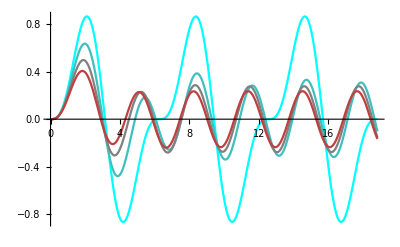

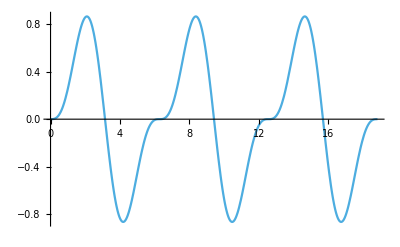

```mathematica
Plot[Evaluate[Table[y[t]/.s2/.β->bb,{bb,0,2,.5}]],{t,0,6 π},PlotStyle->Table[RGBColor[n/2,1- n/2, 1-n/2],{n,0,2,0.5}]]
sa1=Plot[Evaluate[y[t]/.s2/.β->0],{t,0,6 π}]
```

β=0 일 때, 진폭이 가장 큰 것을 알 수 있다.

```mathematica
s2/. β->0//Simplify
```

{{y[t]→1/6 ⅈ ⅇ^(-2 ⅈ t) (-1+ⅇ^(ⅈ t))^3 (1+ⅇ^(ⅈ t))}}

```mathematica
s0=DSolve[{y''[t]+y[t]==Sin[2 t],y[0]==0,y'[0]==0},y[t],t]
```

{{y[t]→1/6 (4 Sin[t]-3 Cos[t] Sin[t]-Cos[3 t] Sin[t]-4 Cos[t] Sin[t]^3)}}

```mathematica
MaxValue[y[t]/. s0,t]-MinValue[y[t]/. s0,t]//N
```

1.73205